```mathematica
data2=
Import["/Users/epersico/Google Drive/GitHub/Map Files/Good Data/20170517/run2/widths/a_0.640000_m_3_n_5_widths.out","Table"];
```

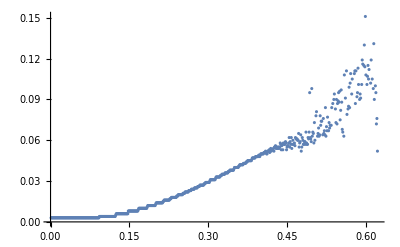

```mathematica
ListPlot[data2]
```

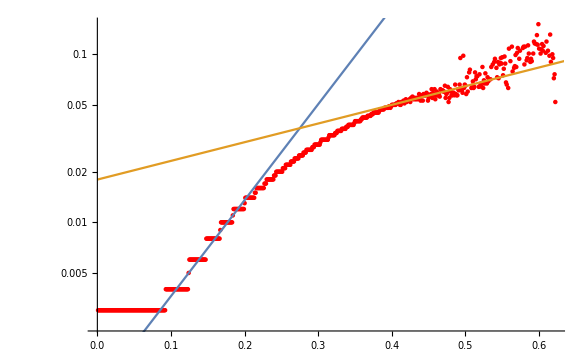

```mathematica
Show[ListLogPlot[data2,PlotStyle->Red],LogPlot[{Exp[line1],Exp[line2]},{x,0,1}]]
```

```mathematica
logdata2=data2;
logdata2[[All,2]]=Log[logdata2[[All,2]]];
```

```mathematica
line1 = Fit[logdata2[[100;;200,All]],{1,x},x]
line2 = Fit[logdata2[[420;;500,All]],{1,x},x]
```

-6.93097+13.1498 x

-4.01928+2.56005 x